## Visualizing Oscillation in the Simple Harmonic Oscillator

We will use a mixture of the 0th and 1st excited states to create a mixture of two states that oscillates.

We’ll work in units where ℏω is the unit of energy and 1/b (see Moore Eq. Q10.20b on p. 160) is the unit of length. By doing that we eliminate ℏω and b everywhere they appear.

### Normalizing the Ground State

First we need to normalize the ground (0th) wavefunction by determining c_0. This comes from a normalization integral you have already done, so we just quote that result for c_0 and ψ_0(x):

```mathematica
cnot = 1/Pi^(1/4); psinot[x_]:= cnot * Exp[-x^2/2]
```

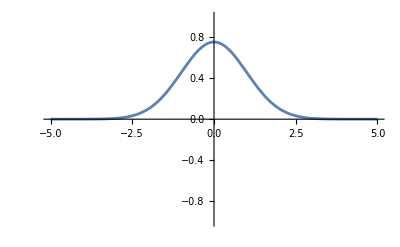

```mathematica
Plot[psinot[x],{x, -5, 5}, PlotRange->{{-5, 5}, {-1, 1}}]
```

It is also good to see the square of the ground state wavefunction and to eyeball whether or not we have gotten it properly normalized:

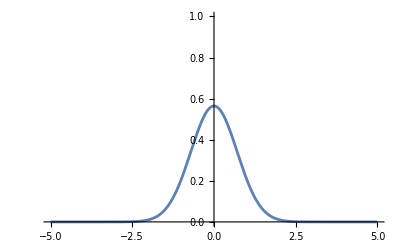

```mathematica
Plot[psinot[x]^2,{x, -5, 5}, PlotRange->{{-5, 5}, {0, 1}}]
```

### Normalizing the First Excited State

We need to normalize the 1st excited state by determining c_1. This is another normalization integral you have already done, so we can just quote  c_1 and ψ_1(x) too:

```mathematica
cone = 2^(1/2)/Pi^(1/4); psione[x_]:= cone * x * Exp[-x^2/2]
```

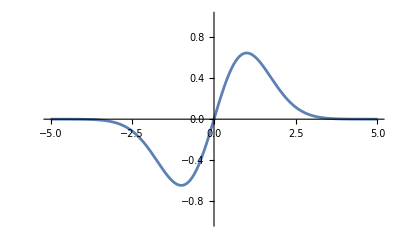

```mathematica
Plot[psione[x],{x, -5, 5}, PlotRange->{{-5, 5}, {-1, 1}}]
```

Let’s look at the square of the first excited state wavefunction and eyeball whether or not we have gotten it properly normalized:

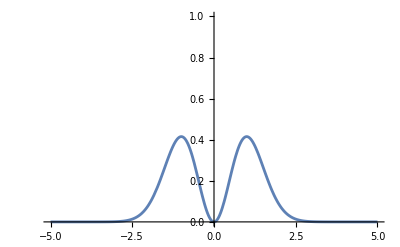

```mathematica
Plot[psione[x]^2,{x, -5, 5}, PlotRange->{{-5, 5}, {0, 1}}]
```

Yes, it is about 4 wide and about 0.25 in average height:

### Making the Mixture

Here’s the cool part. We have ψ_0(x) and ψ_1(x) and now we need to make the mixture (a linear combination):

ψ(x,t)=(e^(-i E_0 t/ℏ)ψ_0(x) +e^(-i E_1 t/ℏ)ψ_1(x))/(√2)

E_0 and E_1 are 1/2 ℏω and 3/2 ℏω, respectively, but since we are working in units where ℏω is the unit of energy, they are just 1/2 and 3/2.

The division by √2 is to make the mixture normalized.

### Squaring the Mixture

What we have written down is a probability amplitude. To get the probability, we have to take its absolute-value squared. The probability amplitude has real and imaginary parts, so to isolate those, we first have to do:

e^(-i E_0 t/ℏ)=cos(E_0 t)/ℏ-isin(E_0 t)/ℏ

e^(-i E_1 t/ℏ)=cos(E_1 t)/ℏ-isin(E_1 t)/ℏ

and then take the real and imaginary parts of the combinations and square them. The upshot is that the real part is,

(cos(E_0 t)/ℏ ψ_0(x) + cos(E_1 t)/ℏ ψ_1(x))/(√2)

and the imaginary part is,

-(sin(E_0 t)/ℏ ψ_0(x) + sin(E_1 t)/ℏ ψ_1(x)/(√2)

and so the squared probability amplitude that we are looking for is,

(|ψ(x,t)|)^2=([cos(E_0 t)/ℏ ψ_0(x) + cos(E_1 t)/ℏ ψ_1(x)]^2+[sin(E_0 t)/ℏ ψ_0(x) + sin(E_1 t)/ℏ ψ_1(x)]^2)/2

### Plotting the Mixture

```mathematica
enot = 1/2; eone = 3/2;
```

```mathematica
timeDependentProbability[x_,t_]:= ((Cos[enot * t]*psinot[x]+Cos[eone * t]*psione[x])^2+(Sin[enot * t]*psinot[x]+Sin[eone * t]*psione[x])^2)/2
```

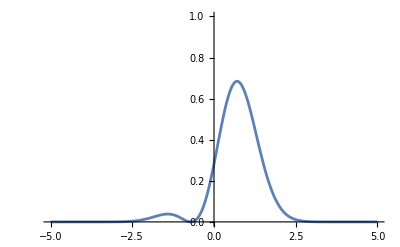

```mathematica
Plot[timeDependentProbability[x,0], {x, -5, 5}, PlotRange->{{-5, 5}, {0, 1}}]
```

```mathematica
Animate[Plot[timeDependentProbability[x,t], {x, -5, 5}, PlotRange->{{-5, 5}, {0, 1}}], {t, 0, 4*Pi}]
```

The lovely thing is that we are starting to see how the classical harmonic motion that we know and love can emerge from the new and bizarre realm of quantum mechanics. We simply had to take a linear combination of some states. Amusingly and pleasantly, we were able to even start seeing the behavior emerge using just the 0th and 1st excited state.